Calculate the data size of an entire image, and the scanning time

```mathematica
μm = 10^-6;
μs=10^-6;
ns = 10^-9;
mm=10^-3;
Tera=10^12;
kHz=10^3;
Mega=10^6;
Giga = 10^9;
byte=8;

bpp=10; (*bits per pixel*)
Δx=0.5μm;(*spatial sampling rate in x and y. Optical resolution is twice this*)
Δz=0.5 μm;(*spatial sampling in z. Optical resolution is twice this*)
Lz=0.5mm;(*section thickness*)
Ltile=0.5mm;(*tile size*)
fx=8 kHz;(*resonant scanner frequency. each line is scanned in 1/fx seconds*)
fy = 1 kHz;
Npix= Ltile/Δx ;(*a tile has a total of Npix by Npix pixels*)
speedx=(Ltile fx)/Δx;(*scanning speed in the x direction [pix/s]*)
speedy=(Ltile fy)/Δx;(*scanning speed in the y direction [pix/s]*)

Ttile[α_] := Npix/α(Npix/speedx+1/speedy);(*total scanning time for each tile [seconds]. It does not include the time to shift between tiles. α is the number of beamlets).*)
Ntiles[L_]:=(L/Ltile)^2(*number of tiles in a plane*)
Npixz[L_]:=L/Δz(*number of pixels in the z axis*)
Npixtotal[L_]:=(L/Δx)^2 L/Δz(*total number of pixels in the sample*)
time[L_,α_]:=Ntiles[L] Npixz[L]Ttile[α] (*total scanning time for the entire sample*)
```

1.25×10^-7

```mathematica
Ltile/Δx
```

1000.

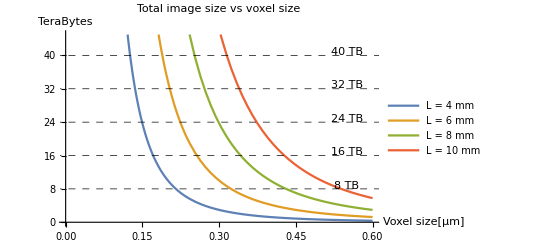

```mathematica
DataSize[L_,Δx_]:=(L/Δx)^3*bpp (*in bits, PER CHANNEL*)
Show[Plot[Evaluate[Table[DataSize[dummy mm,dummy2 μm],{dummy,4,10,2}]/(Tera*byte)],{dummy2,0.1,0.6},AxesOrigin->{0,0},PlotRange->{0,45},PlotLegends-> {"L = 4 mm","L = 6 mm","L = 8 mm","L = 10 mm"},AxesLabel->{"Voxel size[μm]","TeraBytes"},GridLines->{{},{8,16,24,32,40}},GridLinesStyle->Directive[Black, Dashed],PlotLabel->"Total image size vs voxel size"],Graphics[Table[Text[ToString[i]"TB",{0.55,i+.8}],{i,8,40,8}]]]
```

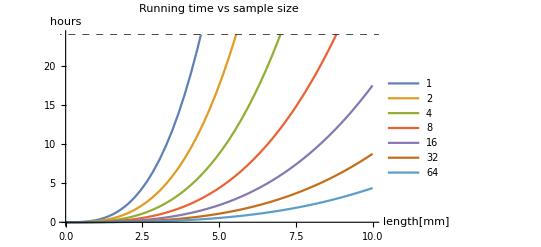

```mathematica
(*Running time PER CHANNEL*)
Plot[Evaluate[Table[time[dummy mm,2^i]/3600,{i,0,6}]],{dummy,0,10},PlotRange->{0,24},AxesLabel->{"length[mm]","hours"},PlotLegends->Table[2^i,{i,0,6}],GridLines->{{},{24}},GridLinesStyle->Directive[Black, Dashed],PlotLabel->"Running time vs sample size"]
```

```mathematica
L=10mm;
Npixtotal[L]
speedx*bpp/(Mega*byte)(*data-saving speed in MB/seconds PER BEAMLET. A commercial HDD writes at 150 MB/s*)
1/Ttile[64](*frames (tiles) per second*)
```

8.×10^12

10.

507.937

How much time does it take to fully transfer a 8TB HDD

```mathematica
HDD=(8 Tera)*byte (*max HDD capacity in bits*)
busrate=10 10^9;(*transfer rate in bps*)
1.*HDD/busrate/3600 (*Time to transfer a 8TB HDD [in hours]*)
```

64000000000000

1.77778

```mathematica
(*Transfer rate [MB/s]*)
(0.5 mm)/(0.4 μm)*8kHz*10 1/(8(1024)^2)*64
```

762.939

```mathematica
(*total data size [TB]*)
3*((10 mm)/(0.5 μm))^3 10 1/(8 (1024)^4)
```

27.2848

```mathematica
(*Runtime [hours]*)
3*(9mm)^3/(0.3 μm)^2 1/(0.5mm*8kHz*64)/3600
```

26.3672

```mathematica
(*source: Murphy*)
nm=10^-9;
n=1.4;(*refractive index*)
na=1.1; (*numerical aperture of the objective*)
λ=800;(*excitation? wavelength*)
(*optical lateral resolution*)
0.325 λ/(√2)na^0.91
(*optical axial resolution*)
0.532 λ/(√2)(1/(n-√(n^2-na^2)))
```

200.505

563.594